```mathematica
scale[list_,f1_,f2_,bins_,s_]:=Module[{δf,δb,tab,bumps},
tab=smoothy[list,bins];
bumps=bumbfinder[tab,bins,s];
δb=bumps[[2,1]]-bumps[[1,1]];
δf=(f2-f1)/δb;
Table[{f1+n*δf,tab[[bumps[[1,1]]+n ]]},{n,0,δb}]];


bumbfinder[smooth_,bins_,s_]:=Module[{diff,out,bumps,s1,s2},
diff=Table[(smooth[[i+1]]-smooth[[i]]),{i,bins-2}];
bumps=FindPeaks[diff,0,s];
s1=Max[smooth];
s2=Max[diff];
Print[ListPlot[{smooth/s1*s2,diff,bumps},PlotStyle->{Automatic,Automatic,PointSize[.03]},PlotRange->Full]];
bumps];

smoothy[list_,bins_]:=Block[{n},
n=Floor[Dimensions[list][[1]]/bins];
Table[Mean[Transpose[list][[2]][[n*i;;n*(1+i)]]],{i,bins-1}]];
```

```mathematica
datno=Import["/home/sander/Downloads/novacbea.dat"];
```

```mathematica
datva=Import["/home/jonathan/Downloads/vacum.dat"];
```

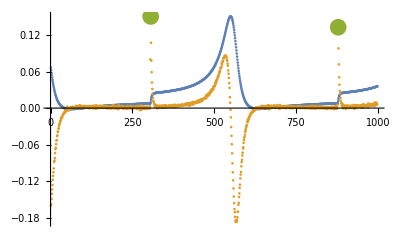

```mathematica
novac=scale[datno,32.73,32.785,1000,.03];
```

```mathematica
vac=scale[datva,32.73,32.785,1000,.03];
```

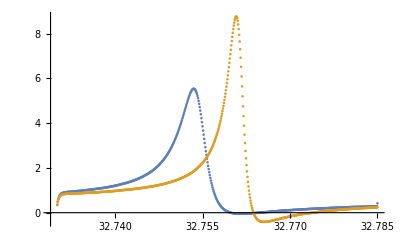

```mathematica
ListPlot[{novac,vac},PlotRange->Full]
```

```mathematica
model=e+a*Sin[b*x+f]+c*Sin[d*x+g]
fit=NonlinearModelFit[datno,model,{a,{b,2},c,{d,4},e,f,g},x]
```

e+a Sin[f+b x]+c Sin[g+d x]

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[-145.545+«1»+66.0479 Sin[4.2668+1.93876 x]]

Fit::fitc: Number of coordinates (1) is not equal to the number of variables (2).

Fit[{{32.73,0.355025},{32.7301,0.505608},{32.7302,0.61291},{32.7303,0.690799},{32.7304,0.749778},{32.7305,0.791811},{32.7306,0.823246},{32.7307,0.846086},{32.7308,0.862786},{32.7309,0.874952},{32.731,0.885267},{32.7311,0.893541},{32.7312,0.899435},{32.7312,0.905707},{32.7313,0.908427},{32.7314,0.910883},{32.7315,0.915814},{32.7316,0.918402},{32.7317,0.922955},{32.7318,0.927092},{32.7319,0.931418},{32.732,0.930927},{32.7321,0.931645},{32.7322,0.934535},{32.7323,0.936254},{32.7324,0.938899},{32.7325,0.940391},{32.7326,0.941638},{32.7327,0.945379},{32.7328,0.949214},{32.7329,0.950687},{32.733,0.953162},{32.7331,0.955146},{32.7332,0.9566},{32.7333,0.95864},{32.7334,0.963004},{32.7335,0.964195},{32.7336,0.967123},{32.7336,0.969352},{32.7337,0.971373},{32.7338,0.97194},{32.7339,0.975208},{32.734,0.979931},{32.7341,0.982368},{32.7342,0.983709},{32.7343,0.988243},{32.7344,0.991851},{32.7345,0.993854},{32.7346,0.99512},{32.7347,0.999427},{32.7348,1.00279},{32.7349,1.0056},{32.735,1.00787},{32.7351,1.00968},{32.7352,1.01229},{32.7353,1.01598},{32.7354,1.01849},{32.7355,1.02181},{32.7356,1.02638},{32.7357,1.02824},{32.7358,1.03043},{32.7359,1.03311},{32.736,1.03738},{32.736,1.04103},{32.7361,1.04401},{32.7362,1.048},{32.7363,1.04941},{32.7364,1.05191},{32.7365,1.05529},{32.7366,1.05992},{32.7367,1.06205},{32.7368,1.06687},{32.7369,1.07133},{32.737,1.07237},{32.7371,1.07805},{32.7372,1.08238},{32.7373,1.08584},{32.7374,1.08816},{32.7375,1.09173},{32.7376,1.09509},{32.7377,1.09802},{32.7378,1.10053},{32.7379,1.10501},{32.738,1.10994},{32.7381,1.11378},{32.7382,1.11659},{32.7383,1.12175},{32.7384,1.12651},{32.7384,1.12998},{32.7385,1.13522},{32.7386,1.13943},{32.7387,1.14274},{32.7388,1.14699},{32.7389,1.15124},{32.739,1.15541},{32.7391,1.16091},{32.7392,1.16539},{32.7393,1.17143},{32.7394,1.17674},{32.7395,1.18137},{32.7396,1.18613},{32.7397,1.19053},{32.7398,1.1958},{32.7399,1.20105},{32.74,1.20636},{32.7401,1.21218},{32.7402,1.21762},{32.7403,1.22202},{32.7404,1.22916},{32.7405,1.23487},{32.7406,1.24129},{32.7407,1.24702},{32.7408,1.25448},{32.7408,1.26228},{32.7409,1.26942},{32.741,1.27401},{32.7411,1.28011},{32.7412,1.2865},{32.7413,1.2929},{32.7414,1.3014},{32.7415,1.30501},{32.7416,1.31077},{32.7417,1.31761},{32.7418,1.32555},{32.7419,1.33292},{32.742,1.34157},{32.7421,1.3485},{32.7422,1.35436},{32.7423,1.3632},{32.7424,1.3687},{32.7425,1.37876},{32.7426,1.3874},{32.7427,1.39477},{32.7428,1.4044},{32.7429,1.41275},{32.743,1.42046},{32.7431,1.42994},{32.7432,1.4392},{32.7432,1.4476},{32.7433,1.45716},{32.7434,1.46784},{32.7435,1.47717},{32.7436,1.4866},{32.7437,1.49816},{32.7438,1.50675},{32.7439,1.51745},{32.744,1.52787},{32.7441,1.54044},{32.7442,1.55319},{32.7443,1.56566},{32.7444,1.57531},{32.7445,1.58802},{32.7446,1.59872},{32.7447,1.61018},{32.7448,1.62401},{32.7449,1.63841},{32.745,1.65225},{32.7451,1.66676},{32.7452,1.67802},{32.7453,1.69217},{32.7454,1.70715},{32.7455,1.72198},{32.7455,1.73715},{32.7456,1.75196},{32.7457,1.7684},{32.7458,1.78474},{32.7459,1.80055},{32.746,1.81636},{32.7461,1.83361},{32.7462,1.85118},{32.7463,1.87107},{32.7464,1.88738},{32.7465,1.90916},{32.7466,1.92846},{32.7467,1.94845},{32.7468,1.96959},{32.7469,1.98999},{32.747,2.01372},{32.7471,2.03446},{32.7472,2.05812},{32.7473,2.08267},{32.7474,2.10502},{32.7475,2.13117},{32.7476,2.15631},{32.7477,2.18365},{32.7478,2.21212},{32.7479,2.23824},{32.7479,2.26879},{32.748,2.29762},{32.7481,2.32701},{32.7482,2.35832},{32.7483,2.39028},{32.7484,2.42523},{32.7485,2.45623},{32.7486,2.49228},{32.7487,2.52792},{32.7488,2.56365},{32.7489,2.60064},{32.749,2.64048},{32.7491,2.68291},{32.7492,2.72288},{32.7493,2.76767},{32.7494,2.81075},{32.7495,2.85705},{32.7496,2.90494},{32.7497,2.95334},{32.7498,3.00542},{32.7499,3.05762},{32.75,3.10951},{32.7501,3.16468},{32.7502,3.2228},{32.7503,3.28065},{32.7503,3.34093},{32.7504,3.40204},{32.7505,3.4673},{32.7506,3.53285},{32.7507,3.59963},{32.7508,3.6676},{32.7509,3.74113},{32.751,3.81287},{32.7511,3.8878},{32.7512,3.9655},{32.7513,4.0425},{32.7514,4.12418},{32.7515,4.20699},{32.7516,4.28905},{32.7517,4.3724},{32.7518,4.45854},{32.7519,4.54372},{32.752,4.62813},{32.7521,4.71416},{32.7522,4.80036},{32.7523,4.88452},{32.7524,4.96742},{32.7525,5.04655},{32.7526,5.12439},{32.7527,5.19736},{32.7527,5.26692},{32.7528,5.32883},{32.7529,5.38541},{32.753,5.43505},{32.7531,5.47599},{32.7532,5.50916},{32.7533,5.52707},{32.7534,5.53595},{32.7535,5.53323},{32.7536,5.51791},{32.7537,5.48667},{32.7538,5.44114},{32.7539,5.38163},{32.754,5.3072},{32.7541,5.21639},{32.7542,5.11082},{32.7543,4.99213},{32.7544,4.86006},{32.7545,4.71477},{32.7546,4.55844},{32.7547,4.39233},{32.7548,4.22129},{32.7549,4.04259},{32.755,3.85806},{32.7551,3.67132},{32.7551,3.48536},{32.7552,3.29831},{32.7553,3.11244},{32.7554,2.92912},{32.7555,2.74978},{32.7556,2.57933},{32.7557,2.4091},{32.7558,2.25001},{32.7559,2.09442},{32.756,1.9484},{32.7561,1.8082},{32.7562,1.67723},{32.7563,1.55132},{32.7564,1.4358},{32.7565,1.32657},{32.7566,1.22172},{32.7567,1.12602},{32.7568,1.03706},{32.7569,0.952029},{32.757,0.874121},{32.7571,0.800785},{32.7572,0.734514},{32.7573,0.670227},{32.7574,0.613099},{32.7575,0.560468},{32.7575,0.511691},{32.7576,0.464443},{32.7577,0.420615},{32.7578,0.381529},{32.7579,0.345012},{32.758,0.310668},{32.7581,0.279384},{32.7582,0.250934},{32.7583,0.222521},{32.7584,0.200286},{32.7585,0.176993},{32.7586,0.157497},{32.7587,0.136225},{32.7588,0.119658},{32.7589,0.101598},{32.759,0.0871457},{32.7591,0.0722782},{32.7592,0.0598288},{32.7593,0.0493442},{32.7594,0.0376504},{32.7595,0.0288471},{32.7596,0.0193258},{32.7597,0.0114859},{32.7598,0.00451503},{32.7599,-0.00275813},{32.7599,-0.00948345},{32.76,-0.0151697},{32.7601,-0.020516},{32.7602,-0.0253144},{32.7603,-0.0286959},{32.7604,-0.0313596},{32.7605,-0.0359691},{32.7606,-0.0379716},{32.7607,-0.0406541},{32.7608,-0.0429022},{32.7609,-0.0437334},{32.761,-0.0425811},{32.7611,-0.0441113},{32.7612,-0.0454714},{32.7613,-0.0458493},{32.7614,-0.0469638},{32.7615,-0.0463026},{32.7616,-0.0468505},{32.7617,-0.045887},{32.7618,-0.0470016},{32.7619,-0.0463215},{32.762,-0.0456603},{32.7621,-0.0457548},{32.7622,-0.0442057},{32.7623,-0.0445458},{32.7623,-0.041901},{32.7624,-0.0405219},{32.7625,-0.040673},{32.7626,-0.0394262},{32.7627,-0.0394262},{32.7628,-0.0357046},{32.7629,-0.0332487},{32.763,-0.0345522},{32.7631,-0.0320775},{32.7632,-0.029206},{32.7633,-0.0274491},{32.7634,-0.0261267},{32.7635,-0.023992},{32.7636,-0.0213472},{32.7637,-0.0187213},{32.7638,-0.0173989},{32.7639,-0.0168511},{32.764,-0.0135262},{32.7641,-0.0107492},{32.7642,-0.0112592},{32.7643,-0.00933232},{32.7644,-0.00493064},{32.7645,-0.00292816},{32.7646,-0.00185135},{32.7647,0.00249366},{32.7647,0.000547849},{32.7648,0.00445835},{32.7649,0.00795325},{32.765,0.00738651},{32.7651,0.00989906},{32.7652,0.0119393},{32.7653,0.0136584},{32.7654,0.0153964},{32.7655,0.0194581},{32.7656,0.0207238},{32.7657,0.0238786},{32.7658,0.0245965},{32.7659,0.0267879},{32.766,0.0277891},{32.7661,0.0301128},{32.7662,0.0325687},{32.7663,0.0368948},{32.7664,0.0408242},{32.7665,0.0431289},{32.7666,0.0436201},{32.7667,0.0465293},{32.7668,0.0484374},{32.7669,0.0491552},{32.767,0.0531224},{32.7671,0.0553705},{32.7671,0.055635},{32.7672,0.06032},{32.7673,0.0621525},{32.7674,0.0645139},{32.7675,0.0648539},{32.7676,0.0661952},{32.7677,0.0697846},{32.7678,0.0726183},{32.7679,0.0713903},{32.768,0.0765099},{32.7681,0.0775489},{32.7682,0.0799859},{32.7683,0.0816483},{32.7684,0.0841798},{32.7685,0.0844253},{32.7686,0.0874857},{32.7687,0.0900739},{32.7688,0.0918685},{32.7689,0.0924164},{32.769,0.0950234},{32.7691,0.0974981},{32.7692,0.0979704},{32.7693,0.100691},{32.7694,0.102315},{32.7695,0.103921},{32.7695,0.107265},{32.7696,0.109778},{32.7697,0.109494},{32.7698,0.112895},{32.7699,0.113216},{32.77,0.114066},{32.7701,0.117447},{32.7702,0.118619},{32.7703,0.118959},{32.7704,0.120376},{32.7705,0.122472},{32.7706,0.124418},{32.7707,0.126723},{32.7708,0.127913},{32.7709,0.128348},{32.771,0.128027},{32.7711,0.1312},{32.7712,0.13222},{32.7713,0.132749},{32.7714,0.136377},{32.7715,0.136377},{32.7716,0.137491},{32.7717,0.139928},{32.7718,0.141534},{32.7718,0.142988},{32.7719,0.145784},{32.772,0.145425},{32.7721,0.147145},{32.7722,0.148184},{32.7723,0.150658},{32.7724,0.151395},{32.7725,0.152888},{32.7726,0.153568},{32.7727,0.154607},{32.7728,0.156779},{32.7729,0.159235},{32.773,0.161672},{32.7731,0.162787},{32.7732,0.16358},{32.7733,0.163977},{32.7734,0.166357},{32.7735,0.168322},{32.7736,0.170003},{32.7737,0.172629},{32.7738,0.172686},{32.7739,0.173838},{32.774,0.17397},{32.7741,0.177163},{32.7742,0.177654},{32.7742,0.178353},{32.7743,0.179543},{32.7744,0.181206},{32.7745,0.183114},{32.7746,0.183832},{32.7747,0.185834},{32.7748,0.187383},{32.7749,0.188252},{32.775,0.188932},{32.7751,0.188913},{32.7752,0.189839},{32.7753,0.190878},{32.7754,0.193561},{32.7755,0.193126},{32.7756,0.194618},{32.7757,0.195034},{32.7758,0.196942},{32.7759,0.19817},{32.776,0.201155},{32.7761,0.202572},{32.7762,0.202893},{32.7763,0.202534},{32.7764,0.203157},{32.7765,0.204801},{32.7766,0.206048},{32.7766,0.208182},{32.7767,0.208919},{32.7768,0.212093},{32.7769,0.211507},{32.777,0.215059},{32.7771,0.216551},{32.7772,0.216003},{32.7773,0.217987},{32.7774,0.218762},{32.7775,0.219574},{32.7776,0.219139},{32.7777,0.22271},{32.7778,0.2239},{32.7779,0.225695},{32.778,0.228207},{32.7781,0.227282},{32.7782,0.228207},{32.7783,0.228717},{32.7784,0.228887},{32.7785,0.227829},{32.7786,0.231513},{32.7787,0.232741},{32.7788,0.234385},{32.7789,0.234876},{32.779,0.23463},{32.779,0.235575},{32.7791,0.235953},{32.7792,0.237804},{32.7793,0.23754},{32.7794,0.238919},{32.7795,0.239807},{32.7796,0.243415},{32.7797,0.244208},{32.7798,0.243906},{32.7799,0.245134},{32.78,0.247816},{32.7801,0.248497},{32.7802,0.249479},{32.7803,0.249668},{32.7804,0.250952},{32.7805,0.250745},{32.7806,0.251746},{32.7807,0.253389},{32.7808,0.252804},{32.7809,0.254258},{32.781,0.255524},{32.7811,0.257451},{32.7812,0.258112},{32.7813,0.257602},{32.7814,0.257867},{32.7814,0.259605},{32.7815,0.259283},{32.7816,0.260152},{32.7817,0.258509},{32.7818,0.259945},{32.7819,0.260984},{32.782,0.263024},{32.7821,0.264006},{32.7822,0.264686},{32.7823,0.264271},{32.7824,0.265877},{32.7825,0.265555},{32.7826,0.266519},{32.7827,0.266519},{32.7828,0.26786},{32.7829,0.269183},{32.783,0.268597},{32.7831,0.268125},{32.7832,0.270599},{32.7833,0.270788},{32.7834,0.271544},{32.7835,0.273017},{32.7836,0.274869},{32.7837,0.274378},{32.7838,0.272394},{32.7838,0.273698},{32.7839,0.275133},{32.784,0.276059},{32.7841,0.279289},{32.7842,0.278024},{32.7843,0.278779},{32.7844,0.281103},{32.7845,0.279875},{32.7846,0.280687},{32.7847,0.282501},{32.7848,0.281745},{32.7849,0.287148},{32.785,0.417895}},{A Sin[x]},{A,x}]

NonlinearModelFit::argrx: NonlinearModelFit called with 2 arguments; 4 arguments are expected.

NonlinearModelFit[{{32.73,0.355025},{32.7301,0.505608},{32.7302,0.61291},{32.7303,0.690799},{32.7304,0.749778},{32.7305,0.791811},{32.7306,0.823246},{32.7307,0.846086},{32.7308,0.862786},{32.7309,0.874952},{32.731,0.885267},{32.7311,0.893541},{32.7312,0.899435},{32.7312,0.905707},{32.7313,0.908427},{32.7314,0.910883},{32.7315,0.915814},{32.7316,0.918402},{32.7317,0.922955},{32.7318,0.927092},{32.7319,0.931418},{32.732,0.930927},{32.7321,0.931645},{32.7322,0.934535},{32.7323,0.936254},{32.7324,0.938899},{32.7325,0.940391},{32.7326,0.941638},{32.7327,0.945379},{32.7328,0.949214},{32.7329,0.950687},{32.733,0.953162},{32.7331,0.955146},{32.7332,0.9566},{32.7333,0.95864},{32.7334,0.963004},{32.7335,0.964195},{32.7336,0.967123},{32.7336,0.969352},{32.7337,0.971373},{32.7338,0.97194},{32.7339,0.975208},{32.734,0.979931},{32.7341,0.982368},{32.7342,0.983709},{32.7343,0.988243},{32.7344,0.991851},{32.7345,0.993854},{32.7346,0.99512},{32.7347,0.999427},{32.7348,1.00279},{32.7349,1.0056},{32.735,1.00787},{32.7351,1.00968},{32.7352,1.01229},{32.7353,1.01598},{32.7354,1.01849},{32.7355,1.02181},{32.7356,1.02638},{32.7357,1.02824},{32.7358,1.03043},{32.7359,1.03311},{32.736,1.03738},{32.736,1.04103},{32.7361,1.04401},{32.7362,1.048},{32.7363,1.04941},{32.7364,1.05191},{32.7365,1.05529},{32.7366,1.05992},{32.7367,1.06205},{32.7368,1.06687},{32.7369,1.07133},{32.737,1.07237},{32.7371,1.07805},{32.7372,1.08238},{32.7373,1.08584},{32.7374,1.08816},{32.7375,1.09173},{32.7376,1.09509},{32.7377,1.09802},{32.7378,1.10053},{32.7379,1.10501},{32.738,1.10994},{32.7381,1.11378},{32.7382,1.11659},{32.7383,1.12175},{32.7384,1.12651},{32.7384,1.12998},{32.7385,1.13522},{32.7386,1.13943},{32.7387,1.14274},{32.7388,1.14699},{32.7389,1.15124},{32.739,1.15541},{32.7391,1.16091},{32.7392,1.16539},{32.7393,1.17143},{32.7394,1.17674},{32.7395,1.18137},{32.7396,1.18613},{32.7397,1.19053},{32.7398,1.1958},{32.7399,1.20105},{32.74,1.20636},{32.7401,1.21218},{32.7402,1.21762},{32.7403,1.22202},{32.7404,1.22916},{32.7405,1.23487},{32.7406,1.24129},{32.7407,1.24702},{32.7408,1.25448},{32.7408,1.26228},{32.7409,1.26942},{32.741,1.27401},{32.7411,1.28011},{32.7412,1.2865},{32.7413,1.2929},{32.7414,1.3014},{32.7415,1.30501},{32.7416,1.31077},{32.7417,1.31761},{32.7418,1.32555},{32.7419,1.33292},{32.742,1.34157},{32.7421,1.3485},{32.7422,1.35436},{32.7423,1.3632},{32.7424,1.3687},{32.7425,1.37876},{32.7426,1.3874},{32.7427,1.39477},{32.7428,1.4044},{32.7429,1.41275},{32.743,1.42046},{32.7431,1.42994},{32.7432,1.4392},{32.7432,1.4476},{32.7433,1.45716},{32.7434,1.46784},{32.7435,1.47717},{32.7436,1.4866},{32.7437,1.49816},{32.7438,1.50675},{32.7439,1.51745},{32.744,1.52787},{32.7441,1.54044},{32.7442,1.55319},{32.7443,1.56566},{32.7444,1.57531},{32.7445,1.58802},{32.7446,1.59872},{32.7447,1.61018},{32.7448,1.62401},{32.7449,1.63841},{32.745,1.65225},{32.7451,1.66676},{32.7452,1.67802},{32.7453,1.69217},{32.7454,1.70715},{32.7455,1.72198},{32.7455,1.73715},{32.7456,1.75196},{32.7457,1.7684},{32.7458,1.78474},{32.7459,1.80055},{32.746,1.81636},{32.7461,1.83361},{32.7462,1.85118},{32.7463,1.87107},{32.7464,1.88738},{32.7465,1.90916},{32.7466,1.92846},{32.7467,1.94845},{32.7468,1.96959},{32.7469,1.98999},{32.747,2.01372},{32.7471,2.03446},{32.7472,2.05812},{32.7473,2.08267},{32.7474,2.10502},{32.7475,2.13117},{32.7476,2.15631},{32.7477,2.18365},{32.7478,2.21212},{32.7479,2.23824},{32.7479,2.26879},{32.748,2.29762},{32.7481,2.32701},{32.7482,2.35832},{32.7483,2.39028},{32.7484,2.42523},{32.7485,2.45623},{32.7486,2.49228},{32.7487,2.52792},{32.7488,2.56365},{32.7489,2.60064},{32.749,2.64048},{32.7491,2.68291},{32.7492,2.72288},{32.7493,2.76767},{32.7494,2.81075},{32.7495,2.85705},{32.7496,2.90494},{32.7497,2.95334},{32.7498,3.00542},{32.7499,3.05762},{32.75,3.10951},{32.7501,3.16468},{32.7502,3.2228},{32.7503,3.28065},{32.7503,3.34093},{32.7504,3.40204},{32.7505,3.4673},{32.7506,3.53285},{32.7507,3.59963},{32.7508,3.6676},{32.7509,3.74113},{32.751,3.81287},{32.7511,3.8878},{32.7512,3.9655},{32.7513,4.0425},{32.7514,4.12418},{32.7515,4.20699},{32.7516,4.28905},{32.7517,4.3724},{32.7518,4.45854},{32.7519,4.54372},{32.752,4.62813},{32.7521,4.71416},{32.7522,4.80036},{32.7523,4.88452},{32.7524,4.96742},{32.7525,5.04655},{32.7526,5.12439},{32.7527,5.19736},{32.7527,5.26692},{32.7528,5.32883},{32.7529,5.38541},{32.753,5.43505},{32.7531,5.47599},{32.7532,5.50916},{32.7533,5.52707},{32.7534,5.53595},{32.7535,5.53323},{32.7536,5.51791},{32.7537,5.48667},{32.7538,5.44114},{32.7539,5.38163},{32.754,5.3072},{32.7541,5.21639},{32.7542,5.11082},{32.7543,4.99213},{32.7544,4.86006},{32.7545,4.71477},{32.7546,4.55844},{32.7547,4.39233},{32.7548,4.22129},{32.7549,4.04259},{32.755,3.85806},{32.7551,3.67132},{32.7551,3.48536},{32.7552,3.29831},{32.7553,3.11244},{32.7554,2.92912},{32.7555,2.74978},{32.7556,2.57933},{32.7557,2.4091},{32.7558,2.25001},{32.7559,2.09442},{32.756,1.9484},{32.7561,1.8082},{32.7562,1.67723},{32.7563,1.55132},{32.7564,1.4358},{32.7565,1.32657},{32.7566,1.22172},{32.7567,1.12602},{32.7568,1.03706},{32.7569,0.952029},{32.757,0.874121},{32.7571,0.800785},{32.7572,0.734514},{32.7573,0.670227},{32.7574,0.613099},{32.7575,0.560468},{32.7575,0.511691},{32.7576,0.464443},{32.7577,0.420615},{32.7578,0.381529},{32.7579,0.345012},{32.758,0.310668},{32.7581,0.279384},{32.7582,0.250934},{32.7583,0.222521},{32.7584,0.200286},{32.7585,0.176993},{32.7586,0.157497},{32.7587,0.136225},{32.7588,0.119658},{32.7589,0.101598},{32.759,0.0871457},{32.7591,0.0722782},{32.7592,0.0598288},{32.7593,0.0493442},{32.7594,0.0376504},{32.7595,0.0288471},{32.7596,0.0193258},{32.7597,0.0114859},{32.7598,0.00451503},{32.7599,-0.00275813},{32.7599,-0.00948345},{32.76,-0.0151697},{32.7601,-0.020516},{32.7602,-0.0253144},{32.7603,-0.0286959},{32.7604,-0.0313596},{32.7605,-0.0359691},{32.7606,-0.0379716},{32.7607,-0.0406541},{32.7608,-0.0429022},{32.7609,-0.0437334},{32.761,-0.0425811},{32.7611,-0.0441113},{32.7612,-0.0454714},{32.7613,-0.0458493},{32.7614,-0.0469638},{32.7615,-0.0463026},{32.7616,-0.0468505},{32.7617,-0.045887},{32.7618,-0.0470016},{32.7619,-0.0463215},{32.762,-0.0456603},{32.7621,-0.0457548},{32.7622,-0.0442057},{32.7623,-0.0445458},{32.7623,-0.041901},{32.7624,-0.0405219},{32.7625,-0.040673},{32.7626,-0.0394262},{32.7627,-0.0394262},{32.7628,-0.0357046},{32.7629,-0.0332487},{32.763,-0.0345522},{32.7631,-0.0320775},{32.7632,-0.029206},{32.7633,-0.0274491},{32.7634,-0.0261267},{32.7635,-0.023992},{32.7636,-0.0213472},{32.7637,-0.0187213},{32.7638,-0.0173989},{32.7639,-0.0168511},{32.764,-0.0135262},{32.7641,-0.0107492},{32.7642,-0.0112592},{32.7643,-0.00933232},{32.7644,-0.00493064},{32.7645,-0.00292816},{32.7646,-0.00185135},{32.7647,0.00249366},{32.7647,0.000547849},{32.7648,0.00445835},{32.7649,0.00795325},{32.765,0.00738651},{32.7651,0.00989906},{32.7652,0.0119393},{32.7653,0.0136584},{32.7654,0.0153964},{32.7655,0.0194581},{32.7656,0.0207238},{32.7657,0.0238786},{32.7658,0.0245965},{32.7659,0.0267879},{32.766,0.0277891},{32.7661,0.0301128},{32.7662,0.0325687},{32.7663,0.0368948},{32.7664,0.0408242},{32.7665,0.0431289},{32.7666,0.0436201},{32.7667,0.0465293},{32.7668,0.0484374},{32.7669,0.0491552},{32.767,0.0531224},{32.7671,0.0553705},{32.7671,0.055635},{32.7672,0.06032},{32.7673,0.0621525},{32.7674,0.0645139},{32.7675,0.0648539},{32.7676,0.0661952},{32.7677,0.0697846},{32.7678,0.0726183},{32.7679,0.0713903},{32.768,0.0765099},{32.7681,0.0775489},{32.7682,0.0799859},{32.7683,0.0816483},{32.7684,0.0841798},{32.7685,0.0844253},{32.7686,0.0874857},{32.7687,0.0900739},{32.7688,0.0918685},{32.7689,0.0924164},{32.769,0.0950234},{32.7691,0.0974981},{32.7692,0.0979704},{32.7693,0.100691},{32.7694,0.102315},{32.7695,0.103921},{32.7695,0.107265},{32.7696,0.109778},{32.7697,0.109494},{32.7698,0.112895},{32.7699,0.113216},{32.77,0.114066},{32.7701,0.117447},{32.7702,0.118619},{32.7703,0.118959},{32.7704,0.120376},{32.7705,0.122472},{32.7706,0.124418},{32.7707,0.126723},{32.7708,0.127913},{32.7709,0.128348},{32.771,0.128027},{32.7711,0.1312},{32.7712,0.13222},{32.7713,0.132749},{32.7714,0.136377},{32.7715,0.136377},{32.7716,0.137491},{32.7717,0.139928},{32.7718,0.141534},{32.7718,0.142988},{32.7719,0.145784},{32.772,0.145425},{32.7721,0.147145},{32.7722,0.148184},{32.7723,0.150658},{32.7724,0.151395},{32.7725,0.152888},{32.7726,0.153568},{32.7727,0.154607},{32.7728,0.156779},{32.7729,0.159235},{32.773,0.161672},{32.7731,0.162787},{32.7732,0.16358},{32.7733,0.163977},{32.7734,0.166357},{32.7735,0.168322},{32.7736,0.170003},{32.7737,0.172629},{32.7738,0.172686},{32.7739,0.173838},{32.774,0.17397},{32.7741,0.177163},{32.7742,0.177654},{32.7742,0.178353},{32.7743,0.179543},{32.7744,0.181206},{32.7745,0.183114},{32.7746,0.183832},{32.7747,0.185834},{32.7748,0.187383},{32.7749,0.188252},{32.775,0.188932},{32.7751,0.188913},{32.7752,0.189839},{32.7753,0.190878},{32.7754,0.193561},{32.7755,0.193126},{32.7756,0.194618},{32.7757,0.195034},{32.7758,0.196942},{32.7759,0.19817},{32.776,0.201155},{32.7761,0.202572},{32.7762,0.202893},{32.7763,0.202534},{32.7764,0.203157},{32.7765,0.204801},{32.7766,0.206048},{32.7766,0.208182},{32.7767,0.208919},{32.7768,0.212093},{32.7769,0.211507},{32.777,0.215059},{32.7771,0.216551},{32.7772,0.216003},{32.7773,0.217987},{32.7774,0.218762},{32.7775,0.219574},{32.7776,0.219139},{32.7777,0.22271},{32.7778,0.2239},{32.7779,0.225695},{32.778,0.228207},{32.7781,0.227282},{32.7782,0.228207},{32.7783,0.228717},{32.7784,0.228887},{32.7785,0.227829},{32.7786,0.231513},{32.7787,0.232741},{32.7788,0.234385},{32.7789,0.234876},{32.779,0.23463},{32.779,0.235575},{32.7791,0.235953},{32.7792,0.237804},{32.7793,0.23754},{32.7794,0.238919},{32.7795,0.239807},{32.7796,0.243415},{32.7797,0.244208},{32.7798,0.243906},{32.7799,0.245134},{32.78,0.247816},{32.7801,0.248497},{32.7802,0.249479},{32.7803,0.249668},{32.7804,0.250952},{32.7805,0.250745},{32.7806,0.251746},{32.7807,0.253389},{32.7808,0.252804},{32.7809,0.254258},{32.781,0.255524},{32.7811,0.257451},{32.7812,0.258112},{32.7813,0.257602},{32.7814,0.257867},{32.7814,0.259605},{32.7815,0.259283},{32.7816,0.260152},{32.7817,0.258509},{32.7818,0.259945},{32.7819,0.260984},{32.782,0.263024},{32.7821,0.264006},{32.7822,0.264686},{32.7823,0.264271},{32.7824,0.265877},{32.7825,0.265555},{32.7826,0.266519},{32.7827,0.266519},{32.7828,0.26786},{32.7829,0.269183},{32.783,0.268597},{32.7831,0.268125},{32.7832,0.270599},{32.7833,0.270788},{32.7834,0.271544},{32.7835,0.273017},{32.7836,0.274869},{32.7837,0.274378},{32.7838,0.272394},{32.7838,0.273698},{32.7839,0.275133},{32.784,0.276059},{32.7841,0.279289},{32.7842,0.278024},{32.7843,0.278779},{32.7844,0.281103},{32.7845,0.279875},{32.7846,0.280687},{32.7847,0.282501},{32.7848,0.281745},{32.7849,0.287148},{32.785,0.417895}},a Sin[c+b x]]